# The Hamiltonian in the Post-Minkowski Approximation

A notebook dedicated to calculating the equations necessary for the Post-Minkowski approximation of the Hamiltonian. This is another method of approximated general relativistic effects, though not as commonly used as the Post-Newtonian approximation.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Basic definitions

This cell evaluates some of the basic definitions that are used in the equations. ndim represents the number of dimension, nbody the number of bodies in the simulation. position is a list containing the x, y, and z (depending on the number of dimensions) positions of each body. p is another vector, containing the x, y, and z components of momentum for each body. m is another list, which contains the masses of all three bodies.

```mathematica
ndim=2;
nbody=2;
If[ndim==2,
position={{qax,qay},{qbx,qby}};
p={{pax,pay},{pbx,pby}};
m={ma,mb};
xdot={{qaxdot1,qaydot1},{qbxdot1,qbydot1}};
pdot={{paxdot1,paydot1},{pbxdot1,pbydot1}};
,
position={{qax,qay,qaz},{qbx,qby,qbz}};
p={{pax,pay,paz},{pbx,pby,pbz}};
m={ma,mb};
xdot={{qaxdot1,qaydot1,qazdot1},{qbxdot1,qbydot1,qbzdot1}};
pdot={{paxdot1,paydot1,pazdot1},{pbxdot1,pbydot1,pbzdot1}};
]
If[nbody==3,
If[ndim==3,
AppendTo[position,{qcx,qcy,qcz}];
AppendTo[p,{pcx,pcy,pcz}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1,qczdot1}];
AppendTo[pdot,{pcxdot1,pcydot1,pczdot1}];
,
AppendTo[position,{qcx,qcy}];
AppendTo[p,{pcx,pcy}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1}];
AppendTo[pdot,{pcxdot1,pcydot1}];
]
]
```

## Functions

These functions listed are used for writing the PM approximation in Mathematica code. They allow for different vector operations. As well, two special functions, mline and y are defined, which correspond to two values in the PM approximation.

```mathematica
Normv[x_List] := Sqrt[x.x]
Normvector[x_List] := x/Normv[x]
rab[a_Integer,b_Integer] := position[[a]] - position[[b]]
Normvsq[x_List] := x.x
nhat[a_Integer,b_Integer] := Normvector[rab[a,b]]
nhatx[a_Integer,b_Integer,i_Integer] := nhat[a,b][[i]]
rdot[a_Integer,b_Integer] := xdot[[a]] - xdot[[b]]
R[a_Integer,b_Integer] :=Normv[rab[a,b]]
psq[a_Integer] := p[[a]].p[[a]]
mline[a_Integer]:=√(m[[a]]^2+psq[a])
y[a_Integer,b_Integer]:=mline[a]^-1 √(m[[a]]^2+(nhat[a,b].p[[a]])^2)
```

## The Hamiltonian

The PM Hamiltonian is defined here, to first order in G. These equations are taken from a 2008 paper by Ledvinka, Schafer, and Bicak. I have broken it up into four separate terms that are summed together to give the equation to first order in G.

```mathematica
W=ConstantArray[0,4];
```

```mathematica
W[[1]]=Sum[mline[a],{a,1,nbody}];
```

```mathematica
W[[2]]=-1/2 G Sum[If[b==a,0,(mline[a]mline[b])/R[a,b](1+psq[a]/mline[a]^2+psq[b]/mline[b]^2)],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[3]]=1/4 G Sum[If[b==a,0,1/R[a,b](7p[[a]].p[[b]]+(p[[a]].nhat[a,b])(p[[b]].nhat[a,b]))],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[4]]=-1/4 G Sum[If[b==a,0,1/R[a,b](mline[a]mline[b])^-1/((y[b,a]+1)^2 y[b,a])(2(2(p[[a]].p[[b]])^2(p[[b]].nhat[b,a])^2-2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])psq[b]+(p[[a]].nhat[b,a])^2 psq[b]^2-(p[[a]].p[[b]])^2 psq[b])1/mline[b]^2+2(-psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+(p[[a]].p[[b]])^2-(p[[a]].nhat[b,a])^2 psq[b])+(-3psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+8(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+psq[a]psq[b]-3(p[[a]].nhat[b,a])^2 psq[b])y[b,a])],{a,1,nbody},{b,1,nbody}];
```

```mathematica
newtonH=1/2 Sum[psq[a]/m[[a]],{a,1,nbody}]-G/2 Sum[If[b==a,0,(m[[a]]m[[b]])/R[a,b]],{a,1,nbody},{b,1,nbody}];
```

Here, the equations are summed into one equation, PM1. Then, using the properties of the Hamiltonian, the equations for change in momentum, pdot0, are found by taking the negative derivative of PM1 with respect to each position component and the equations for change in position, qdot0, are found by taking the derivative of PM1 with respect to each momentum component. These equations are then converted into C code and exported as text files, which can be copied into a C code for calculating this Hamiltonian.

```mathematica
<<Format1.m
<<Optimize.m
```

```mathematica
PM1=Sum[W[[a]],{a,1,4}];
```

```mathematica
pdot0=Table[D[-PM1,position[[ibody]][[idim]]],{ibody,1,nbody},{idim,1,ndim}];
qdot0 =Table[D[PM1,p[[ibody]][[idim]] ],{ibody,1,nbody},{idim,1,ndim}];
```

```mathematica
newtonc=CAssign[newtonH,newtonH,"OptimizationSymbol"->o];
PMc = CAssign[PM1,PM1,"OptimizationSymbol"->o];
pdot0c = CAssign[pdot0,pdot0,"OptimizationSymbol"->z];
qdot0c = CAssign[qdot0,qdot0,"OptimizationSymbol"->o];
```

```mathematica
equations={qdot0,pdot0,PM1};
eq=CAssign[equations,equations,"OptimizationSymbol"->o];
```

```mathematica
Export["newtonHamiltonian.txt",newtonc]
Export["equations.txt",eq]
Export["PMHamiltonian.txt",PMc]
Export["pdot0.txt",pdot0c]
Export["qdot0.txt",qdot0c]
```

newtonHamiltonian.txt

equations.txt

PMHamiltonian.txt

pdot0.txt

qdot0.txt

## Calculating Conservation of Angular Momentum

There are many different papers on the method of calculating initial conditions to obtain a circular orbit in PM approximations. This sections contains many of those methods, several of which were not effective with our code.

### Antonelli et al., 2019

This method comes from a paper on a 3rd order PM approximation; we only use the first order terms. There are some issues here. As the distance between the bodies gets smaller, pθ becomes a complex value. This is actually expected though, as this solution is the same as the Schwarzschild solution, except it inherently assumes that c=1. The imaginary solutions represent where the orbit would be unstable and one object would be pulled past the event horizon of the other.

```mathematica
M=ma+mb;μ=(ma mb)/M;u=(G M)/r;l=pθ/(G M μ);
HPM1[pθ_,r_]=(1-2u)(1+l^2 u^2);(*This is the Hamiltonian to first order*)
prdot0=D[HPM1[pθ,r],r];(*Here the derivative with respect to r gives the change in tangential momentum. We want this to be 0 for a circular orbit.*)

userG=1/(16 Pi);userm1=1;userm2=1;userr=5;userC=1;
newtonianZero={{√((G (ma mb)^2 r)/(ma+mb)),0}}/.{r  ->userr,ma->userm1,mb->userm2,G->userG};(*The*)
newtonianZero//N
Solve[prdot0==0,pθ];          
pθ/.{%[[2,1]]}//Simplify
%/.{r->userr,ma->userm1,mb->userm2,G->userG}//N
```

{{0.223016,0.}}

(√(-G (ma+mb)))/(√(((ma+mb)^2 (3 G (ma+mb)-r))/(ma^2 mb^2 r^2)))

0.225726

### Bern et al., 2019

This comes from another paper on a 3PM approximation. The quantities p1 and p2 defined in the paper are unclear as to what the refer to, so it’s difficult to tell whether or not it’s being solved correctly. As well as this, the equation is too complex to be solved analytically for pθ, and so it must be solved numerically using actual values instead of stand-in variables. The function and its first two derivatives are exported as c code, to be used in another code for approximating the zeroes of the equation. This equation has also not yet proved to be effective.
UPDATE: According to Cheung et al., 2019, p1*p2 = E1*E2 + p^2, where p is the canonical momentum.

```mathematica
E1=√(pcan^2+ma^2);E2=√(pcan^2+mb^2);v=(ma mb)/M^2;Etot=E1+E2;ξ=(E1 E1)/Etot^2;γ=Etot/M;σ0=(p1 p2)/(ma mb);
σ=(E1 E2+pcan^2)/(ma mb);
cpol={(v^2 M^2)/(γ^2 ξ)(1-2 σ^2)};
V[pcan_,r_]=cpol[[1]] G/r;
H[pcan_,r_]=√(pcan^2+ma^2)+√(pcan^2+mb^2)+V[pcan,r]//Simplify;
Hpol=H[√(pr^2+pθ^2/r^2),r];
prdot=D[Hpol,r];
init[pθ_]:=Simplify[prdot/.pr->0]
init[pθ]/.{ma->userm1,mb->userm2,r->userr,G->userG}//Simplify
Solve[%==0,pθ,Reals]
```

(15625+14375 pθ^2+1200 pθ^4+24 pθ^6-800 π pθ^2 (25+pθ^2)^(3/2))/(10000 π (25+pθ^2)^2)

{{pθ→-√(Root0.0520Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,3]0.05196177541327646)},{pθ→√(Root0.0520Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,3]0.05196177541327646)},{pθ→-√(Root1.09 × 10^4Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,4]10941.231850897295)},{pθ→√(Root1.09 × 10^4Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,4]10941.231850897295)}}

-1/(√(ma^2+x^2/r^2))-1/(√(mb^2+x^2/r^2))+(4 G (x^2+r^2 √(ma^2+x^2/r^2) √(mb^2+x^2/r^2)) (ma^2 r^2+mb^2 r^2+2 x^2+2 r^2 √(ma^2+x^2/r^2) √(mb^2+x^2/r^2)))/(r^3 (ma^2 r^2+x^2) √(ma^2+x^2/r^2) √(mb^2+x^2/r^2))+(2 G ma^2 mb^2 (1-(2 (x^2/r^2+√(ma^2+x^2/r^2) √(mb^2+x^2/r^2))^2)/(ma^2 mb^2)))/(r (ma^2+x^2/r^2)^2)+(G (ma^2 mb^2 r^4+4 x^4+2 r^2 x^2 (ma^2+mb^2+2 √(ma^2+x^2/r^2) √(mb^2+x^2/r^2))))/(r x^2 (ma^2 r^2+x^2))

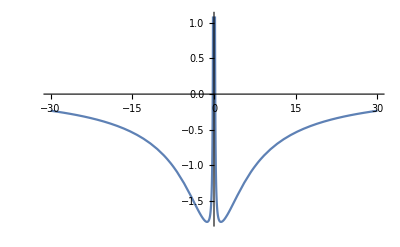

o4=pow(r,-2.);
o5=x*x;
o6=o4*o5;
o3=ma*ma;
o7=o3+o6;
o8=1./sqrt(o7);
o10=mb*mb;
o11=o10+o6;
o12=1./sqrt(o11);
o15=r*r;
o16=o15*o3;
o19=sqrt(o7);
o20=sqrt(o11);
o28=1/r;
o17=o16+o5;
o18=1/o17;
init0=-o12-o8+2.*G*o10*o28*o3*(1.-2.*pow(ma,-2.)*pow(mb,-2.)*pow(o19*o20+o6,2.))*pow(o7,-2.\
)+4.*G*o12*o18*(o15*o19*o20+o5)*(o10*o15+o16+2.*o15*o19*o20+2.*o5)*o8*pow(r,-3.)+G*o18*o28\
*pow(x,-2.)*(2.*o15*(o10+2.*o19*o20+o3)*o5+o10*o3*pow(r,4.)+4.*pow(x,4.));

o3=pow(r,-2.);
o5=x*x;
o6=o3*o5;
o4=ma*ma;
o7=o4+o6;
o10=mb*mb;
o11=o10+o6;
o17=sqrt(o7);
o21=sqrt(o11);
o20=1./sqrt(o7);
o18=1./sqrt(o11);
o28=r*r;
o27=pow(r,-3.);
o29=o28*o4;
o30=o29+o5;
o31=1/o30;
o12=pow(o11,-1.5);
o36=o17*o21*o28;
o37=o36+o5;
o43=o10*o28;
o44=2.*o5;
o45=2.*o17*o21*o28;
o46=o29+o43+o44+o45;
o48=pow(r,-5.);
o8=pow(o7,-1.5);
o24=o17*o21;
o25=o24+o6;
o14=1/r;
o51=pow(o30,-2.);
o67=2.*o17*o21;
o68=o10+o4+o67;
o73=pow(r,4.);
o74=o10*o4*o73;
o75=pow(x,4.);
o76=4.*o75;
o77=2.*o28*o5*o68;
o78=o74+o76+o77;
init0prime=(-2.*G*o14*o51*o78)/x+o12*o3*x-4.*G*o12*o20*o31*o37*o46*o48*x-8.*G*o18*o20*o27*o\
37*o46*o51*x+o3*o8*x-4.*G*o18*o31*o37*o46*o48*o8*x+4.*G*o18*o20*o27*o31*o46*(2.*x+o17*o18*\
x+o20*o21*x)+4.*G*o18*o20*o27*o31*o37*(4.*x+2.*o17*o18*x+2.*o20*o21*x)-8.*G*o10*o27*o4*x*(\
1.-2.*(o25*o25)*pow(ma,-2.)*pow(mb,-2.))*pow(o7,-3.)-8.*G*o14*o25*(2.*o3*x+o17*o18*o3*x+o2\
0*o21*o3*x)*pow(o7,-2.)-2.*G*o14*o31*o78*pow(x,-3.)+G*o14*o31*pow(x,-2.)*(4.*o28*o68*x+2.*\
o28*o5*(2.*o17*o18*o3*x+2.*o20*o21*o3*x)+16.*pow(x,3.));

o4=x*x;
o6=pow(r,-2.);
o5=ma*ma;
o7=o4*o6;
o8=o5+o7;
o3=pow(r,-4.);
o13=mb*mb;
o14=o13+o7;
o25=1./sqrt(o14);
o24=1./sqrt(o8);
o27=sqrt(o8);
o29=sqrt(o14);
o37=1/r;
o38=pow(o8,-2.);
o17=pow(o14,-1.5);
o11=pow(o8,-1.5);
o19=pow(r,-3.);
o39=2.*o6*x;
o40=o25*o27*o6*x;
o41=o24*o29*o6*x;
o42=o39+o40+o41;
o52=o27*o29;
o53=o52+o7;
o20=r*r;
o21=o20*o5;
o22=o21+o4;
o23=1/o22;
o32=4.*x;
o33=2.*o25*o27*x;
o34=2.*o24*o29*x;
o35=o32+o33+o34;
o63=o20*o27*o29;
o64=o4+o63;
o66=pow(r,-5.);
o26=2.*x;
o28=o25*o27*x;
o30=o24*o29*x;
o31=o26+o28+o30;
o77=o13*o20;
o78=2.*o4;
o79=2.*o20*o27*o29;
o80=o21+o77+o78+o79;
o69=pow(o22,-2.);
o15=pow(o14,-2.5);
o85=pow(r,-7.);
o9=pow(o8,-2.5);
o55=pow(o8,-3.);
o97=pow(ma,-2.);
o98=pow(mb,-2.);
o99=o53*o53;
o100=-2.*o97*o98*o99;
o101=1.+o100;
o113=2.*o25*o27*o6*x;
o114=2.*o24*o29*o6*x;
o115=o113+o114;
o117=2.*o27*o29;
o118=o117+o13+o5;
o123=pow(x,3.);
o124=16.*o123;
o125=2.*o115*o20*o4;
o126=4.*o118*o20*x;
o127=o124+o125+o126;
o93=pow(o22,-3.);
o104=pow(x,-2.);
o131=pow(r,4.);
o132=o13*o131*o5;
o133=pow(x,4.);
o134=4.*o133;
o135=2.*o118*o20*o4;
o136=o132+o134+o135;
init0prime2=8.*G*o19*o23*o24*o25*o31*o35-3.*o15*o3*o4-8.*G*o101*o13*o19*o5*o55+o11*o6+o17*o\
6-8.*G*o37*o38*o53*(2.*o24*o25*o3*o4-o17*o27*o3*o4-o11*o29*o3*o4+2.*o6+o25*o27*o6+o24*o29*\
o6)+4.*G*o19*o23*o24*o25*(4.+2.*o25*o27+2.*o24*o29+4.*o24*o25*o4*o6-2.*o17*o27*o4*o6-2.*o1\
1*o29*o4*o6)*o64+6.*G*o104*o136*o37*o69+4.*G*o19*o23*o24*o25*(2.+o25*o27+o24*o29+2.*o24*o2\
5*o4*o6-o17*o27*o4*o6-o11*o29*o4*o6)*o80-4.*G*o17*o23*o24*o64*o66*o80-4.*G*o11*o23*o25*o64\
*o66*o80-8.*G*o19*o24*o25*o64*o69*o80+16.*G*o17*o24*o4*o64*o66*o69*o80+16.*G*o11*o25*o4*o6\
4*o66*o69*o80+8.*G*o11*o17*o23*o4*o64*o80*o85+12.*G*o15*o23*o24*o4*o64*o80*o85-3.*o3*o4*o9\
+12.*G*o23*o25*o4*o64*o80*o85*o9+8.*G*o136*o37*o93+32.*G*o19*o24*o25*o4*o64*o80*o93-(4.*G*\
o127*o37*o69)/x+64.*G*o19*o42*o53*o55*x-8.*G*o17*o23*o24*o35*o64*o66*x-8.*G*o11*o23*o25*o3\
5*o64*o66*x-16.*G*o19*o24*o25*o35*o64*o69*x-8.*G*o17*o23*o24*o31*o66*o80*x-8.*G*o11*o23*o2\
5*o31*o66*o80*x-16.*G*o19*o24*o25*o31*o69*o80*x+G*o104*o23*o37*(4.*o118*o20+48.*o4+2.*o20*\
o4*(4.*o24*o25*o3*o4-2.*o17*o27*o3*o4-2.*o11*o29*o3*o4+2.*o25*o27*o6+2.*o24*o29*o6)+8.*o11\
5*o20*x)-8.*G*o37*o38*(o42*o42)+48.*G*o101*o13*o4*o5*o66*pow(o8,-4.)+6.*G*o136*o23*o37*pow\
(x,-4.)-4.*G*o127*o23*o37*pow(x,-3.);

init0.txt

initprime.txt

initprime2.txt

```mathematica
init0=(init[x] r^3)/x^2/.pθ->x//Simplify
Plot[init0/.{r->userr,ma->userm1,mb->userm2,G->userG},{x,-30,30}]
init0prime=D[init0,x];
init0prime2=D[init0prime,x];
initc=CAssign[init0,init0,"OptimizationSymbol"->o]
initcprime=CAssign[init0prime,init0prime,"OptimizationSymbol"->o]
initcprime2=CAssign[init0prime2,init0prime2,"OptimizationSymbol"->o]
Export["init0.txt",initc]
Export["initprime.txt",initcprime]
Export["initprime2.txt",initcprime2]
```

### Schwarzschild Solution

Many papers posit that using the Schwarzschild solution to solve for the angular momentum in a conserved system works for a Post-Minkowski approximation.

```mathematica
rs=(2G M)/c^2
Lz=√((μ^2 c^2 rs r^2)/(2r-3rs))//Simplify
Lz/.{c->userC,G->userG,ma->userm1,mb->userm2,r->userr}//N
%/newtonianZero[[1,1]]//N
```

(2 G (ma+mb))/c^2

√(-(c^2 G ma^2 mb^2 r^2)/((ma+mb) (3 G (ma+mb)-c^2 r)))

0.225726

1.01215

### Second Antonelli et al., 2019 solution

This is another possible solution that comes from Antonelli et al., that will likely be more complicated. This will only evaluate correctly if this notebook is set to be only two bodies.

```mathematica
γ0=(PM1^2-ma^2-mb^2)/(2ma mb);Γ=PM1/M;p0sq=μ^2(γ0^2-1)/Γ^2;f1=2 μ^2 M (2 γ0^2-1)/Γ;
p0sq+G/R[1,2] f1/.{qax->500,qbx->-500,qay->0,qby->0,pax->0,pbx->0,ma->userm1,mb->userm2,G->userG,pby->-pay}
Solve[%==pay^2,pay,Reals]//N
```

(-1+1/4 (-2+(2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π))^2)^2)/((2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π))^2)+(-1+1/2 (-2+(2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π))^2)^2)/(8000 (2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π)) π)

{{pay→-0.0169995},{pay→0.0169995},{pay→-745.03},{pay→745.03},{pay→-14361.6},{pay→14361.6}}

### Schaefer Solution

This is simply taking the N-body Hamiltonian that’s derived in this paper, and solving it for initial data by itself.

(-pθ^2 (√(ma^2+pθ^2/r^2)+√(mb^2+pθ^2/r^2)) (r^2)^(3/2) (pθ^2+ma^2 r^2) (pθ^2+mb^2 r^2)+G (12 pθ^8+6 ma^2 mb^2 pθ^2 (ma^2+mb^2+2 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2)) r^6+ma^4 mb^4 r^8+pθ^6 (18 ma^2 r^2+18 mb^2 r^2+12 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^2)+pθ^4 (4 ma^4 r^4+4 mb^4 r^4+12 mb^2 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^4+ma^2 (27 mb^2 r^4+12 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^4))))/(√(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^5 √(r^2) (pθ^2+ma^2 r^2) (pθ^2+mb^2 r^2))

(15625+24 pθ^6-400 pθ^4 (-3+2 π √(25+pθ^2))-625 pθ^2 (-23+32 π √(25+pθ^2)))/(10000 π (25+pθ^2)^2)

{{pθ→-√(Root0.0520Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,3]0.05196177541327646)},{pθ→√(Root0.0520Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,3]0.05196177541327646)},{pθ→-√(Root1.09 × 10^4Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,4]10941.231850897295)},{pθ→√(Root1.09 × 10^4Root[244140625+449218750 #1+(244140625-10000000000 π^2) #1^2+(35250000-1200000000 π^2) #1^3+(2130000-48000000 π^2) #1^4+(57600-640000 π^2) #1^5+576 #1^6&,4]10941.231850897295)}}

0.04559025133217690979753828

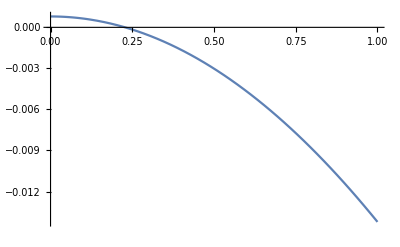

```mathematica
PM1/.{qax->r Cos[θ]+qbx,qay->r Sin[θ]+qby,pax->pcan Cos[θ],pay->pcan Sin[θ],pbx->-pcan Cos[θ],pby->-pcan Sin[θ]};
%/.pcan->√(pr^2+pθ^2/r^2);
PM1rdot[pθ_]=D[%,r];
PM1rdot[pθ]/.{pr->0,θ->0}//Simplify
%/.{ma->userm1,mb->userm2,G->userG,r->userr}//Simplify
Solve[%==0,pθ,Reals]
N[(pθ/.%[[2,1]])/userr,25]
Plot[PM1rdot[pθ]/.{pr->0,θ->0,ma->userm1,mb->userm2,G->userG,r->userr},{pθ,0,1}]



(*PM1/.{qay->0,qby->0,pax->0,pbx->0,pby->-pay,qax->r+qbx}
PM1rdot=D[%,r]
PM1rdot/.{ma->userm1,mb->userm2,G->userG,r->userr}//Simplify
Solve[%==0,pay,Reals]*)
```